```mathematica
Quit;
ClearAll;
Needs["VariationalMethods`"]
cm=72/2.54;
ConfigureMaTeX["pdfLaTeX"->"/usr/bin/pdflatex","Ghostscript"->"/usr/local/bin/gs"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
<<MaTeX`
```

ConfigureMaTeX[pdfLaTeX→/usr/bin/pdflatex,Ghostscript→/usr/local/bin/gs]

ConfigureMaTeX::shdw: Symbol "ConfigureMaTeX" appears in multiple contexts {"MaTeX`", "Global`"}; definitions in context "MaTeX`" may shadow or be shadowed by other definitions.

```mathematica
Action=Sqrt[r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]])v'[x]^2]; (*Action functional (eqn4.5)*)
```

```mathematica
FullSimplify[Eliminate[{EulerEquations[Action,v[x],x],EulerEquations[Action,r[x],x],r[x]^4/rmin^2==r[x]^2+2 r'[x] v'[x]-(-m[v[x]]+r[x]^2) v'[x]^2},m[v[x]]]] ;(*We can eliminate one of the two EL equations using eqn4.6 which can be derived from reparametrrising the action in terms of v and then minimising*)
```

```mathematica
(*This function does the following: takes arguments r0,t,b,Col, where Col defines the Line colour of the output figures.
1. Produce a inital solution Sol to calculate ℓ/2
2. Produce SolL, i.e. the solution for v,r running from -ℓ/2 to -x0
3. Produce 3 plots of the geodesics in the rx,vx,rv planes, output as a list {rx,vx,rv}
4.Integrate to find geodesic length*)
f[r0_,t_,b_,Col_]:=Module[{a,m0,Eqn1,Eqn2,r,x,v,rmax,xmax,x0,Sol,ℓ,SolL,gr1,gr2,gr3,LInt,dot,scal,gr4,temp1,AH,y},
a=1/3;
m0=1;
m[v_]:=m0(Tanh[v/a]+1)/2; (*define the mass function*)
Eqn1=r0^2(r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]])v'[x]^2)-r[x]^4;
Eqn2=r[x]^2-r[x]^2 v'[x]^2-r[x]v''[x]+2v'[x]r'[x];
rmax=100;
x0=r0/(2(rmax)^2);
xmax=100;
Sol=NDSolve[{Eqn1==0,Eqn2==0,r[x0]==rmax,v[x0]==t,v'[x0]==-rmax/r0+b/r0},{r,v},{x,x0,xmax}];
ℓ=2*x/.Last[Quiet[FindMinimum[v[x]/.Sol,{x,x0,x0,xmax}]]];
SolL=NDSolve[{Eqn1==0,Eqn2==0,r[-ℓ/2]==rmax,v[-ℓ/2]==t,v'[-ℓ/2]==-rmax/r0+b/r0},{r,v},{x,-ℓ/2,-x0},"ExtrapolationHandler"->{Indeterminate &}];
gr1=Plot[{Evaluate[r[x]/.SolL],Evaluate[Sqrt[m[v[x]]]/.SolL]},{x,-ℓ/2,ℓ/2},PlotStyle->{Col,{Dashed,Black}},PlotRange->All];
gr2=Plot[Evaluate[v[x]/.SolL],{x,-ℓ/2,ℓ/2},PlotStyle->{Col},PlotRange->All];
gr3=ParametricPlot[{Evaluate[{v[x],r[x]}/.SolL],Evaluate[{v[x],Sqrt[m[v[x]]]}/.SolL]},{x,-ℓ/2,-x0},AspectRatio->1/GoldenRatio,PlotRange->All,PlotStyle->{Col,{Black,Dashed}}];
LInt=2/r0*(NIntegrate[r[x]^2/.SolL,{x,-ℓ/2,-x0}])-2Log[r[-ℓ/2]/.SolL[[1]]];
gr4=ParametricPlot3D[Evaluate[{x,v[x],r[x]}/.SolL],{x,-ℓ/2,-x0},PlotRange->All,PlotStyle->Col];
AH=ParametricPlot3D[Evaluate[{y,v[x],Sqrt[m[v[x]]]}/.SolL],{x,-ℓ/2,-x0},{y,-ℓ/2,ℓ/2},PlotRange->All,PlotStyle->{LightBlue,Opacity[0.5]}];
{gr1,gr2,gr3,ℓ,LInt,gr4,AH}
]
```

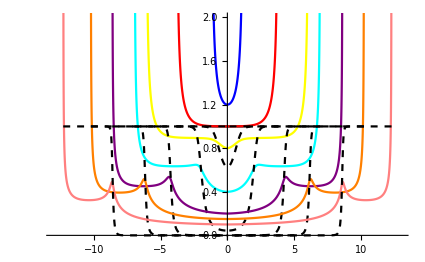

```mathematica
(*Create multiple plots with varying parameters*)
rx1=Part[Quiet[f[1.2,6,0,Blue]],1];
rx2=Part[f[1.0,6,0.001,Red],1];
rx3=Part[f[0.8,6,0.198029,Yellow],1];
rx4=Part[f[0.4,6,0.59405,Cyan],1];
rx5=Part[f[0.2,6,0.79204,Purple],1];
rx6=Part[f[0.15,6,0.841522,Orange],1];
rx7=Part[f[0.1,6,0.89099,Pink],1];
(*Stick the plots together then mirror each plot in the x=0 plane*)
imagexr=Show[{rx1,rx2,rx3,rx4,rx5,rx6,rx7},{rx1,rx2,rx3,rx4,rx5,rx6,rx7}/.L_Line:>{GeometricTransformation[L,ReflectionTransform[{1,0}]]},PlotRange->{{-13,13},{0.0,2.0}},BaseStyle->texStyle,AxesLabel->MaTeX/@{"$x$","$r$"},AxesOrigin->{0,0},ImageSize->15cm]
```

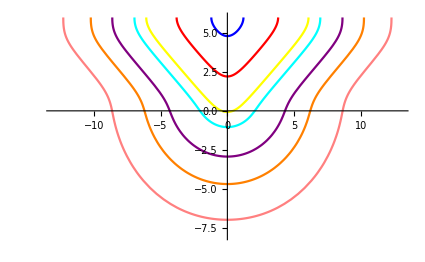

```mathematica
vx1=Part[Quiet[f[1.2,6,0,Blue]],2];
vx2=Part[f[1.0,6,0.001,Red],2];
vx3=Part[f[0.8,6,0.198029,Yellow],2];
vx4=Part[f[0.4,6,0.59405,Cyan],2];
vx5=Part[f[0.2,6,0.79204,Purple],2];
vx6=Part[f[0.15,6,0.841522,Orange],2];
vx7=Part[f[0.1,6,0.89099,Pink],2];

imagexv=Show[{vx1,vx2,vx3,vx4,vx5,vx6,vx7},{vx1,vx2,vx3,vx4,vx5,vx6,vx7}/.L_Line:>{GeometricTransformation[L,ReflectionTransform[{1,0}]]},PlotRange->{{-13,13},{-8,6}},AxesOrigin->{0,0},BaseStyle->texStyle,AxesLabel->MaTeX/@{"$x$","$v$"},ImageSize->15cm]
```

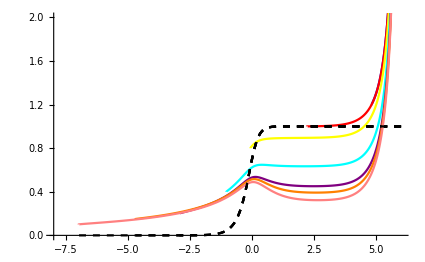

```mathematica
rv1=Part[Quiet[f[1.2,6,0,Blue]],3];
rv2=Part[f[1.0,6,0.001,Red],3];
rv3=Part[f[0.8,6,0.198029,Yellow],3];
rv4=Part[f[0.4,6,0.59405,Cyan],3];
rv5=Part[f[0.2,6,0.79204,Purple],3];
rv6=Part[f[0.15,6,0.841522,Orange],3];
rv7=Part[f[0.1,6,0.89099,Pink],3];

imagerv=Show[{rv1,rv2,rv3,rv4,rv5,rv6,rv7},PlotRange->{{-8,6},{0.0,2.0}},AxesOrigin->{-8,0},BaseStyle->texStyle,AxesLabel->MaTeX/@{"$v$","$r$"},ImageSize->15cm]
```

```mathematica
xrv1=Part[Quiet[f[1.2,6,0,Blue]],6];
xrv2=Part[f[1.0,6,0.001,Red],6];
xrv3=Part[f[0.8,6,0.198029,Yellow],6];
xrv4=Part[f[0.4,6,0.59405,Cyan],6];
xrv5=Part[f[0.2,6,0.79204,Purple],6];
xrv6=Part[f[0.15,6,0.841522,Orange],6];
xrv7=Part[f[0.1,6,0.89099,Pink],6];
AHP=Part[f[0.1,6,0.89099,Pink],7];

imagexrv=Show[{xrv1,xrv2,xrv3,xrv4,xrv5,xrv6,xrv7},{xrv1,xrv2,xrv3,xrv4,xrv5,xrv6,xrv7}/.L_Line:>{GeometricTransformation[L,ReflectionTransform[{1,0,0}]]},AHP,PlotRange->{{-13,13},{-8,6},{0.0,2.0}},BoxRatios->{1, 1, 1},BaseStyle->texStyle,AxesLabel->MaTeX/@{"$x$","$v$","$r$"},ImageSize->12cm]
```

-Graphics3D-

```mathematica
(*Begin Horrible List*)
(*t=0*)
Clear[gl0,gl2,gl1,gl3,gl4,gl5,gl6,gl7,gl8];
Quiet[gl0=Flatten[f[2,0,0,Blue][[{4,5}]],1];
gl1=Flatten[f[1.2,0,0.0009,Blue][[{4,5}]],1];
(*gl2=Quiet[Flatten[f[1.0,0,0.001,Red][[{4,5}]],1]];*)
gl3=Flatten[f[0.8,0,0.04999,Yellow][[{4,5}]],1];
gl4=Flatten[f[0.4,0,0.05,Cyan][[{4,5}]],1];
gl5=Flatten[f[0.2,0,0.1,Purple][[{4,5}]],1];
gl6=Flatten[f[0.15,0,0.1,Orange][[{4,5}]],1];
gl7=Flatten[f[0.1,0,0.1,Pink][[{4,5}]],1];
gl8=Flatten[f[0.01,0,0.1,Pink][[{4,5}]],1]];
Lt0=ListCurvePathPlot[{ {1,0},gl0,gl1,gl3,gl4,gl5,gl6,gl7,gl8},PlotRange->All,AxesOrigin->{0,0},AspectRatio->1/2,InterpolationOrder->3,PlotStyle->{Green}];
```

```mathematica
(*t=2*)
Clear[gl0,gl2,gl1,gl3,gl4,gl5,gl6,gl7,gl8];
Quiet[gl0=Flatten[f[2,2,0,Blue][[{4,5}]],1];
gl1=Flatten[f[1.2,2,0.02,Blue][[{4,5}]],1];
gl2=Flatten[f[1.0,2,0.07,Red][[{4,5}]],1];
gl3=Flatten[f[0.8,2,0.23,Yellow][[{4,5}]],1];
gl4=Flatten[f[0.4,2,0.57,Cyan][[{4,5}]],1];
gl5=Flatten[f[0.2,2,0.699,Purple][[{4,5}]],1];
gl6=Flatten[f[0.15,2,0.722,Orange][[{4,5}]],1];
gl7=Flatten[f[0.1,2,0.74,Pink][[{4,5}]],1];
gl8=Flatten[f[0.01,2,0.77,Pink][[{4,5}]],1]];
Lt2=ListCurvePathPlot[{ {1,0},gl0,gl1,gl2,gl3,gl4,gl5,gl6,gl7,gl8},PlotRange->All,AxesOrigin->{0,0},AspectRatio->1/2,InterpolationOrder->3,PlotStyle->{Cyan}];
```

```mathematica
(*t=4*)
Clear[gl0,gl1,gl2,gl3,gl4,gl5,gl6,gl7,gl8];
Quiet[gl0=Flatten[f[2,4,0,Blue][[{4,5}]],1];
gl1=Flatten[f[1.2,4,0,Blue][[{4,5}]],1];
gl2=Flatten[f[1.0,4,0.01,Red][[{4,5}]],1];
gl3=Flatten[f[0.8,4,0.199,Yellow][[{4,5}]],1];
gl4=Flatten[f[0.4,4,0.5939,Cyan][[{4,5}]],1];
gl5=Flatten[f[0.2,4,0.79,Purple][[{4,5}]],1];
gl6=Flatten[f[0.15,4,0.839,Orange][[{4,5}]],1];
gl7=Flatten[f[0.1,4,0.886,Pink][[{4,5}]],1];
gl8=Flatten[f[0.01,4,0.956,Pink][[{4,5}]],1]];
Lt4=ListCurvePathPlot[{ {1,0},gl0,gl1,gl2,gl3,gl4,gl5,gl6,gl7,gl8},PlotRange->All,AxesOrigin->{0,0},AspectRatio->1/2,InterpolationOrder->3,PlotStyle->{Purple}];
```

```mathematica
(*t=6*)
Clear[gl0,gl2,gl1,gl3,gl4,gl5,gl6,gl7,gl8];
Quiet[gl0=Flatten[f[2,6,0,Blue][[{4,5}]],1];
gl1=Flatten[f[1.2,6,0,Blue][[{4,5}]],1];
gl2=Flatten[f[1.0,6,0.001,Red][[{4,5}]],1];
gl3=Flatten[f[0.8,6,0.198029,Yellow][[{4,5}]],1];
gl4=Flatten[f[0.4,6,0.59405,Cyan][[{4,5}]],1];
gl5=Flatten[f[0.2,6,0.79204,Purple][[{4,5}]],1];
gl6=Flatten[f[0.15,6,0.841522,Orange][[{4,5}]],1];
gl7=Flatten[f[0.1,6,0.89099,Pink][[{4,5}]],1];
gl8=Flatten[f[0.01,6,0.9792,Pink][[{4,5}]],1]];
Lt6=ListCurvePathPlot[{ {1,0},gl0,gl2,gl1,gl3,gl4,gl5,gl6,gl7,gl8},PlotRange->All,AxesOrigin->{0,0},AspectRatio->1/2,InterpolationOrder->3,PlotStyle->{Red}];
```

```mathematica
(*t=8*)
Clear[gl0,gl2,gl1,gl3,gl4,gl5,gl6,gl7,gl8];
Quiet[gl0=Flatten[f[2,8,0,Blue][[{4,5}]],1];
gl1=Flatten[f[1.2,8,0.001,Blue][[{4,5}]],1];
gl2=Flatten[f[1.0,8,0.001,Red][[{4,5}]],1];
gl3=Flatten[f[0.8,8,0.19802,Yellow][[{4,5}]],1];
gl4=Flatten[f[0.4,8,0.564059,Cyan][[{4,5}]],1];
gl5=Flatten[f[0.2,8,0.792079,Purple][[{4,5}]],1];
gl6=Flatten[f[0.15,8,0.841583,Orange][[{4,5}]],1];
gl7=Flatten[f[0.1,8,0.891087,Pink][[{4,5}]],1];
gl8=Flatten[f[0.01,8,0.980178,Pink][[{4,5}]],1]];
Lt8=ListCurvePathPlot[{ {1,0},gl0,gl1,gl2,gl3,gl4,gl5,gl6,gl8},PlotRange->All,AxesOrigin->{0,0},AspectRatio->1/2,InterpolationOrder->3,PlotStyle->{Blue}];
(*End Horrible list*)
```

```mathematica
(*Complile all graphs*)
β=2Pi;
TherRes=Plot[2Log[β/Pi Sinh[(Pi*ℓ)/β]],{ℓ,0,60},PlotStyle->{Black,Dashed},PlotRange->All];
VacRes=Plot[2Log[ℓ],{ℓ,0,60},PlotStyle->{Black, DotDashed},PlotRange->All];
imageLl=Show[{Lt0,Lt2,Lt4,Lt6,Lt8,TherRes,VacRes},PlotRange->{{0,40},{0,25}},BaseStyle->texStyle,AxesLabel->MaTeX/@{"\ell","$\~L$(t,\ell)"},AspectRatio->0.7,ImageSize->25cm]
```

-Graphics-

```mathematica
Export["Lvslads3.png", imageLl]
Export["xrads3.png", imagexr]
Export["xvads3.png", imagexv]
Export["xrvads3.png", imagexrv]
Export["rvads3.png", imagerv]
```

Lvslads3.png

xrads3.png

xvads3.png

xrvads3.png

rvads3.png